## LOESS fitting example

Import the module.

```mathematica
<<"Loess.wl"
```

Generate some data.

```mathematica
SeedRandom[10];
x=Range[0,15,.1];
y=Sin[x]+RandomReal[{-.5,.5},Length[x]];
data=Transpose[{x,y}];
```

Perform two LOESS fits, one with the default order 2 quadratic fit, and the second with a order 1 linear fit.

```mathematica
loessfit=Loess[data,20,2];
loessdata=Transpose[{x,loessfit/@x}];
loessfitlinear=Loess[data,20,1];
loessdatalinear=Transpose[{x,loessfitlinear/@x}];
```

Plot the actual model, the noisy data, and the two fits.

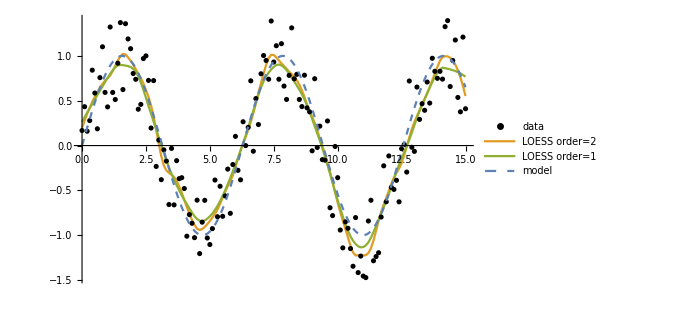

```mathematica
cc=ColorData[97];
p1=ListPlot[{data,loessdata,loessdatalinear},PlotStyle->{Black,cc[2],cc[3]},Joined->{False,True,True},PlotLegends->{"data","LOESS order=2", "LOESS order=1"}];
p2=Plot[{Sin[x]},{x,0,15},PlotStyle->{Dashed},PlotLegends->{"model"}];
p3=Show[{p1,p2},PlotRange->All,ImageSize->500]
```

Fitting with order zero turns the LOESS fit into a weighted moving average.  The weights are determined by the tri-cube weighting function.

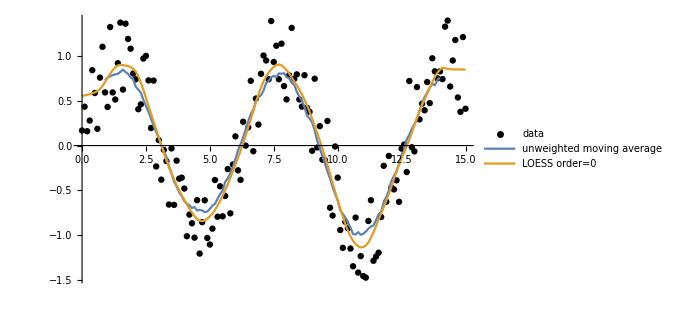

```mathematica
num=20;
loessfit0=Loess[data,num,0];
loessdata0=Transpose[{x,loessfit0/@x}];
movingaverage={x[[num/2;;-(num/2+1)]],MovingAverage[y,num]}ᵀ;
p4=ListPlot[data,PlotStyle->Black,PlotLegends->{"data"}];
p5=ListLinePlot[{movingaverage, loessdata0},PlotLegends->{"unweighted moving average","LOESS order=0"}];
Show[{p4,p5},ImageSize->500]
```